α

{x^2,x^3/2}

β

{s,s^2}

{c1,c2}

Lpart

c1 ((3 x^2)/4-x^3/10)+c2 (-x^2/10+(11 x^3)/24)

Rpart

(ⅇ^x-x) (x^2/2+x^3/6)

l

{(3 c1)/4-c2/10,-c1/5+(11 c2)/12}

r

{1/2 (ⅇ^x-x),1/3 (ⅇ^x-x)}

{{c1→590/801 (ⅇ^x-x),c2→140/267 (ⅇ^x-x)}}

{ⅇ^x-x+590/801 (ⅇ^x-x) x^2+70/267 (ⅇ^x-x) x^3}

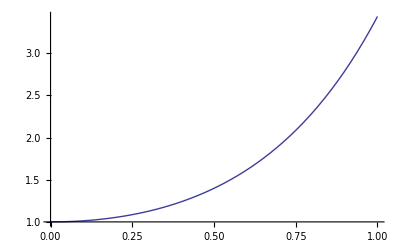

```mathematica
f[x_]=Exp[x]-x;
K[x_,s_]=x (Exp[x s]-1);
λ=1;
n=2;
a=0;
b=1;
tayl = Series[K[x,s],{x,0,n+1},{s,0,n+1}];
Print["α"]
α=Table[Coefficient[tayl,s,i],{i,1,n}]
Print["β"]
β=Table[Coefficient[tayl,α[[i]]],{i,1,n}]

(*c=Table[∫_0^1 β[[i]]y[s]ⅆs,{i,1,n}];*)
c=Table[ToExpression[ "c"<>ToString[i]],{i,1,n}]
A=Table[Table[∫_a^b β[[i]](α[[j]]/.x->s)ⅆs,{j,1,n}],{i,1,n}];
Print["Lpart"]
Lpart=∑_(j=1)^n c[[j]](α[[j]]-∑_(i=1)^n α[[i]]A[[i,j]])
Print["Rpart"]
Rpart = λ f[x]∑_(i=1)^n α[[i]]∫_a^b β[[i]]ⅆs
Print["l"]
l=Table[Coefficient[Lpart,α[[i]]],{i,1,n}]
Print["r"]
r=Table[Coefficient[Rpart/f[x],α[[i]]]*f[x],{i,1,n}]
sol=Solve[l==r,Table[c[[i]],{i,1,n}]]//Simplify
y[x_]=f[x]+λ∑_(i=1)^n α[[i]]c[[i]]/.sol
Plot[y[x],{x,0,1}]
```